```mathematica
fA[x_]=If[x<-1,0,(x+1)^2/2]
```

If[x<-1,0,1/2 (x+1)^2]

```mathematica
fB[x_]=If[x<1,-(x-1)^2/2+1,1]
```

If[x<1,-1/2 (x-1)^2+1,1]

```mathematica
f[x_]=If[x<0,fA[x],fB[x]]
```

If[x<0,fA[x],fB[x]]

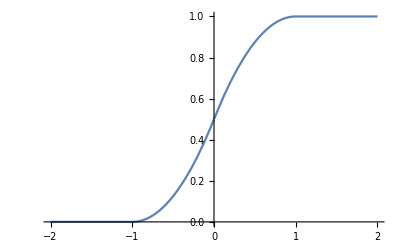

```mathematica
Plot[f[x],{x,-2,2}]
```